# Análisis de entropía

## Inicialización

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Información de los paquetes cargados

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Cargar base de datos

```mathematica
database = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices","DJI_DAX_MXX_NIKKEI_dataset.wdx"}]];
```

## Calculo de entropía continua

```mathematica
HackLog[x_] := If[x>0, Log[x], 0];
ContinuousEntropy[data_]:=Block[{dist},
 dist= SmoothKernelDistribution[data];
-NIntegrate[PDF[dist,x]*HackLog[PDF[dist,x]/PDF[UniformDistribution[{Min[data],Max[data]}],x]],{x,Min[data],Max[data]}]
];
ContinuousEntropySafe[data_]:=Mean@Table[ContinuousEntropy[data],4];
```

```mathematica
market = First[database];
```

```mathematica
ContinuousEntropy[Abs[TrendReturns[market["Prices"]]]]
```

-1.45071

```mathematica
ProgressTable[{database[[i]]["Name"],ContinuousEntropy[Abs[TrendReturns[database[[i]]["Prices"]]]]},{i,1,Length[database]}]
```

{{DAX,-1.45071},{DJIA,-1.68963},{IPC,-1.20152},{NIKKEI225,-1.57514}}

## Sub-optimal trader vs optimal

```mathematica
RandomTradeLengths[maxRun_,totalLength_]:=MapAt[UpTo,NestWhile[Append[#,RandomInteger[{1,maxRun}]]&,{},Total[#]<totalLength&],-1];
RandomLongTradesOverPrices[prices_,maxRun_]:=Returns[Map[First,TakeList[prices,RandomTradeLengths[maxRun,Length[prices]]]]];

LongReturn[{p1_,p2_}]:=Log[p2]-Log[p1];
ShortReturn[{p1_,p2_}]:=Log[p1]-Log[p2];
RandomLongShortTradesOverPrices[prices_,maxRun_]:=Block[{tradePrices,longBuys,shortSales},
tradePrices = Map[First,TakeList[prices,RandomTradeLengths[maxRun,Length[prices]]]];
longBuys = Map[LongReturn,Partition[tradePrices,2,1][[1;;-1;;2]]];
shortSales = Map[ShortReturn,Partition[tradePrices,2,1][[2;;-1;;2]]];

Join[longBuys,shortSales]
];
```

DAX

```mathematica
market = First[database];
```

```mathematica
prices = market["Prices"];
```

```mathematica
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[prices,15],1000];
```

```mathematica
randomTradesEntropies = ProgressParallelMap[ContinuousEntropy,randomTrades];
```

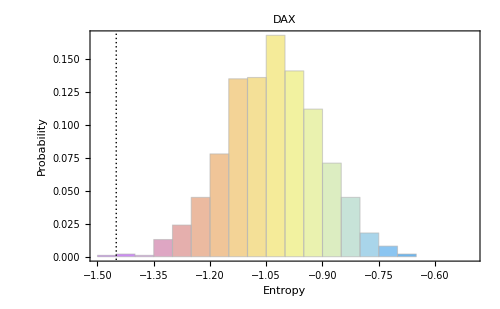

```mathematica
Histogram[
randomTradesEntropies,
Automatic,
"Probability",
GridLines->{{-1.45},{}},
PlotRange->{{-1.5,-0.5},Automatic},
PlotLabel->market["Name"],
PlotTheme->"Monochrome",
FrameLabel->{Style["Entropy",15], Style["Probability",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500,
ChartStyle->"Pastel"
]
```

DJIA

```mathematica
market = database[[2]];
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
randomTradesEntropies = ProgressParallelMap[ContinuousEntropy,randomTrades];
```

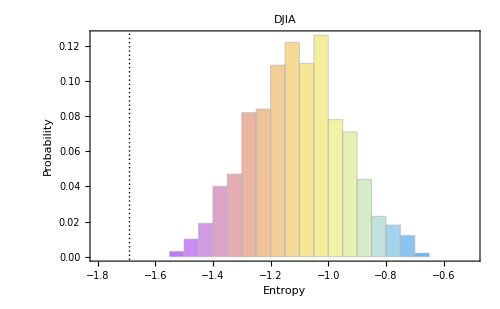

```mathematica
Histogram[
randomTradesEntropies,
Automatic,
"Probability",
GridLines->{{-1.689},{}},
PlotRange->{{-1.8,-0.5},Automatic},
PlotLabel->market["Name"],
PlotTheme->"Monochrome",
FrameLabel->{Style["Entropy",15], Style["Probability",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500,
ChartStyle->"Pastel"
]
```

IPC

```mathematica
market = database[[3]];
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
randomTradesEntropies = ProgressParallelMap[ContinuousEntropy,randomTrades];
```

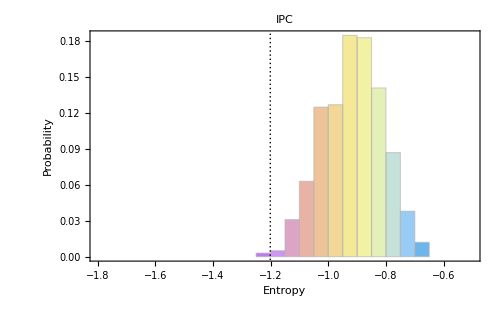

```mathematica
Histogram[
randomTradesEntropies,
Automatic,
"Probability",
GridLines->{{-1.201},{}},
PlotRange->{{-1.8,-0.5},Automatic},
PlotLabel->market["Name"],
PlotTheme->"Monochrome",
FrameLabel->{Style["Entropy",15], Style["Probability",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500,
ChartStyle->"Pastel"
]
```

Nikkei

```mathematica
market = database[[4]];
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
```

```mathematica
randomTradesEntropies = ProgressParallelTable[ContinuousEntropy[randomTrades[[i]]],{i,1,Length[randomTrades]}];
```

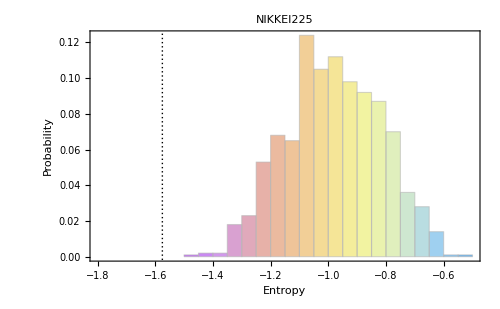

```mathematica
Histogram[
randomTradesEntropies,
Automatic,
"Probability",
GridLines->{{-1.57514464610976},{}},
PlotRange->{{-1.8,-0.5},Automatic},
PlotLabel->market["Name"],
PlotTheme->"Monochrome",
FrameLabel->{Style["Entropy",15], Style["Probability",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500,
ChartStyle->"Pastel"
]
```

## Kullback-Leibler divergence

Calcular entropia KullbackLeibler y comparar con el trader óptimo y con los retornos.

```mathematica
HackLog2[x_] := If[x =!= ComplexInfinity ∧ 0.000001<x<10^6, Log[x], 0.0];

KullbackLeibler[data1_, data2_] := Module[{p,q},
p = SmoothKernelDistribution[data1];
q = SmoothKernelDistribution[data2];
Quiet[NIntegrate[PDF[p, x]*(HackLog2[PDF[p, x]]-HackLog2[PDF[q, x]]),{x, -∞, ∞}]]
];
```

### DAX

```mathematica
market = First[database];
```

```mathematica
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
```

```mathematica
tr = Abs[TrendReturns[market["Prices"]]];
```

```mathematica
klRandomTrades = ProgressMap[{Total[#],KullbackLeibler[#, tr]}&,randomTrades];
```

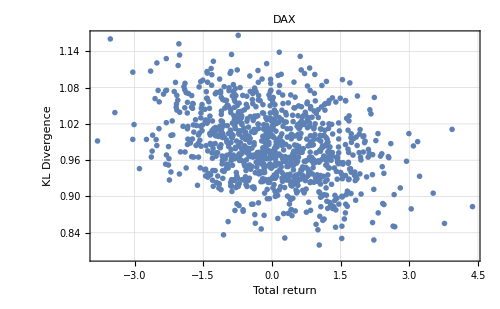

```mathematica
ListPlot[
klRandomTrades,
PlotLabel->market["Name"],
PlotTheme->"Monochrome",
FrameLabel->{Style["Total return",15], Style["KL Divergence",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500
]
```

### DJIA

```mathematica
market = database[[2]];
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
tr = Abs[TrendReturns[market["Prices"]]];
klRandomTrades = ProgressMap[{Total[#],KullbackLeibler[#, tr]}&,randomTrades];
```

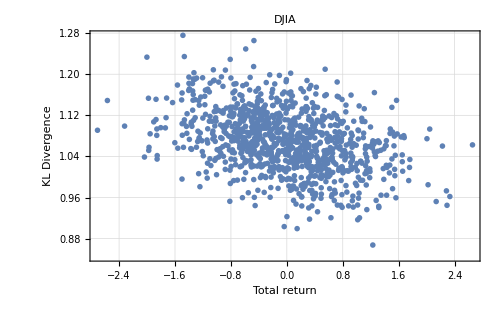

```mathematica
ListPlot[
klRandomTrades,
PlotLabel->market["Name"],
PlotTheme->"Monochrome",
FrameLabel->{Style["Total return",15], Style["KL Divergence",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500
]
```

### IPC

```mathematica
market = database[[3]];
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
tr = Abs[TrendReturns[market["Prices"]]];
klRandomTrades = ProgressMap[{Total[#],KullbackLeibler[#, tr]}&,randomTrades];
```

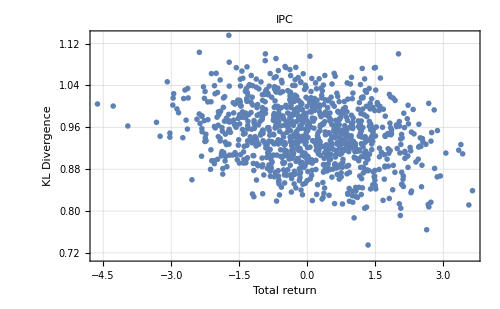

```mathematica
ListPlot[
klRandomTrades,
PlotLabel->market["Name"],
PlotTheme->"Monochrome",
FrameLabel->{Style["Total return",15], Style["KL Divergence",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500
]
```

### Nikkei

```mathematica
market = database[[4]];
randomTrades= ProgressTable[RandomLongShortTradesOverPrices[market["Prices"],15],1000];
tr = Abs[TrendReturns[market["Prices"]]];
klRandomTrades = ProgressMap[{Total[#],KullbackLeibler[#, tr]}&,randomTrades];
```

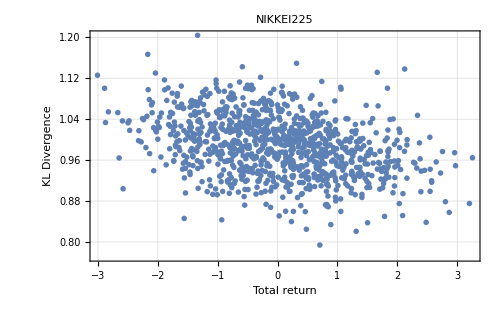

```mathematica
ListPlot[
klRandomTrades,
PlotLabel->market["Name"],
PlotTheme->"Monochrome",
FrameLabel->{Style["Total return",15], Style["KL Divergence",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500
]
```